# Física Experimental

## An Introduction to Error Analysis - John R. Taylor

## Chapter 2: How to report and use Uncertainties

### Summary

(Measured value of x) = x_best

## Chapter 4: Statistical Analysis of Random Uncerteinties

### Definitions

```mathematica
mean[data_List]:=Total[data]/Length[data];//N
standardDeviation[data_List]:=Sqrt[Total[(data-ConstantArray[mean[data],Length[data]])^2]/(Length[data]-1)]//N
standardDeviation2[data_List]:=Sqrt[Total[(data-ConstantArray[mean[data],Length[data]])^2]/Length[data]]//N
```

Definitions used:
- Mean: x̄=∑_i x_i
- Standard deviation: √(1/(N-1)∑_i (x_i-x̄)^2)

### Exercises

#### Quick check 4.1

```mathematica
mean[{21,24,25,22}]
```

23

```mathematica
standardDeviation[{21,24,25,22}]//N
```

1.82574

#### Quick check 4.2

```mathematica
mean[{15,17,18,14,16}]
```

16

```mathematica
standardDeviation[{15,17,18,14,16}]/Length[{15,17,18,14,16}]//N
```

0.316228

#### Exercise 4.5

```mathematica
anotherSD[data_List]:=Total[data^2]-(Total[data])^2/Length[data]
data={11,13,12};
standardDeviation[data]^2*(Length[data]-1)
anotherSD[data]
```

2

2

#### Exercise 4.6

```mathematica
data={10,13,8,15,8,13,14,13,19,8,13,13,7,8,6,8,11,12,8,7};
mean[data]//N
standardDeviation[data]//N
√mean[data]//N
```

10.7

3.40433

3.27109

A una cifra significativa, la desviación estándar y la regla del cuadrado de la media dan la misma incerteza. En otras palabras, la regla del cuadrado de la media funciona bien.

#### Exercise 4.13

```mathematica
data={8.16,8.14,8.12,8.16,8.18,8.10,8.18,8.18,8.18,8.24,8.16,8.14,8.17,8.18,8.21,8.12,8.12,8.17,8.06,8.10,8.12,8.10,8.14,8.09,8.16,8.16,8.21,8.14,8.16,8.13};
mean[data]
standardDeviation[data]
```

8.14933

0.0392984

A continuación calculamos la cantidad de datos que esperaría que se encuentren fuera del 68% de confianza:

```mathematica
0.32*Length[data]
```

9.6

Pero en realidad hay:

```mathematica
If[#≥8.15+0.04|| #≤8.15-0.04,#,Nothing]&/@data//Length
```

8

Deberíamos esperar que afuera del 95% hayan

```mathematica
0.05*Length[data]
```

1.5

Pero en realidad hay:

```mathematica
If[#≥8.15+0.08|| #≤8.15-0.08,#,Nothing]&/@data//Length
```

2

#### Exercise 4.19

```mathematica
data={10,13,8,15,8,13,14,13,19,8,13,13,7,8,6,8,11,12,8,7};
mean[data]//N
standardDeviation[data]/√Length[data]//N
```

10.7

0.761232

La respuesta sería 10.7±0.2 partículas por cada 2 segundos.

```mathematica
data={10,13,8,15,8,13,14,13,19,8,13,13,7,8,6,8,11,12,8,7};
Total[data]/20//N
√Total[data]/20//N
```

10.7

0.731437

#### Exercise 4.22

```mathematica
data={{57.3,61.1,73.2,83.7,95.0},{1.521,1.567,1.718,1.835,1.952}};AppendTo[data,4 π^2 data[[1]]/data[[2]]^2];
TableForm[data,TableHeadings->{{"Longitud, l (cm)","Tiempo, T (s)","Gravedad, g (cm/s)"}, None}]
```

Longitud, l (cm) | 57.3 | 61.1 | 73.2 | 83.7 | 95.
Tiempo, T (s) | 1.521 | 1.567 | 1.718 | 1.835 | 1.952
Gravedad, g (cm/s) | 977.813 | 982.343 | 979.094 | 981.325 | 984.291

Utilizando propagación de errores:

Media e incerteza de la longitud

```mathematica
mean[data[[1]]]
```

74.06

```mathematica
74.06*0.003
```

0.22218

Media e incerteza del tiempo

```mathematica
mean[data[[2]]]
```

1.7186

```mathematica
1.7186*0.02
```

0.034372

```mathematica
g[l_,T_]:=(4 π^2 l)/T^2
```

```mathematica
g[74.1,1.72]
```

988.829

```mathematica
√(Abs[D[g[l,T],l]]δl+Abs[D[g[l,T],T]]δT)/.{l->74.1,δl->0.2,T->1.72,δT->0.03}
```

6.09614

Respuesta: 9.89±0.06 m/s^2.

```mathematica
mean[data[[3]]]
```

980.973

```mathematica
standardDeviation[data[[3]]]/√Length[data[[3]]]
```

1.15164

Respuesta: 9.81±0.01 m/s^2.

## Chapter 5: The Normal Distribution

### Quick check 5.1

```mathematica
joeGrades={2,0,7,4,7};
Range[0,4].joeGrades/Total[joeGrades]//N
```

2.7

```mathematica
Integrate[1/(2 √(2π))Exp[-(x-10)^2/(2 4)],{x,7,13}]//N
```

0.866386

La probabilidad de que una medición de x se encuentre entre 7 y 13 es 84%. Por lo tanto, la probabilidad de que una medición caiga afuera de este rango es 16%.

```mathematica
(75-60)/12//N
```

1.25

```mathematica
√(9^2+3^2)//N
```

9.48683

## Chapter 7: Weighted Averages

### Quick check 7.1

```mathematica
xA=10;σA=0.5;xB=12;σB=1;wA=1/σA^2;wB=1/σB^2;
(wA xA+wB xB)/(wA+wB)
```

10.4

### Problem 7.1

```mathematica
Total[#[[1]]/(#[[2]])^2&/@{{1.4,0.5},{1.2,0.2},{1.0,0.25},{1.3,0.2}}]
```

84.1

```mathematica
Total[1/(#[[2]])^2&/@{{1.4,0.5},{1.2,0.2},{1.0,0.25},{1.3,0.2}}]
```

70.

```mathematica
84.1/70//N
```

1.20143

```mathematica
1/70//N
```

0.0142857

La respuesta final es 1.20±0.01.

### Problem 7.3

### (a)

```mathematica
xA=334;σA=1;xB=336;σB=2;wA=1/σA^2;wB=1/σB^2;
(wA xA+wB xB)/(wA+wB)//N
1/(√(wA+wB))//N
```

334.4

0.894427

### (b)

```mathematica
xA=334;σA=1;xB=336;σB=5;wA=1/σA^2;wB=1/σB^2;
(wA xA+wB xB)/(wA+wB)//N
1/(√(wA+wB))//N
```

334.077

0.980581

No vale la pena incluir la segunda medición.

### Problem 7.5

```mathematica
xA=72;σA=8;xB=78;σB=5;wA=1/σA^2;wB=1/σB^2;
(wA xA+wB xB)/(wA+wB)//N
1/(√(wA+wB))//N
```

76.3146

4.23999

La respuesta final es 76±4 ohms.

## Chapter 8: Least-Squares Fitting

### Definitions

```mathematica
Delta[x_]:=Length[x]Total[x^2]-Total[x]^2;
Aconstant[x_,y_]:=(x.x Total[y]-Total[x]Total[MapThread[Times,{x,y}]])/Delta[x]//N;
Bconstant[x_,y_]:=(Length[x]Total[MapThread[Times,{x,y}]]-Total[x]Total[y])/Delta[x]//N
SigmaY[x_,y_]:=√(1/(Length[x]-2)Total[(y-Aconstant[x,y]-Bconstant[x,y]x)^2])//N
SigmaA[x_,y_]:=SigmaY[x,y] √((x.x)/Delta[x])
SigmaB[x_,y_]:=SigmaY[x,y] √(Length[x]/Delta[x])
```

### Quick Check 8.1

```mathematica
A=(2 (6+6))/(3 2)
B=(3 (6))/(3 2)
```

4

3

### Problem 8.2

```mathematica
x={-3,-1,1,3};y={3,4,8,9};
Aconstant[x,y]
Bconstant[x,y]
```

6.

1.1

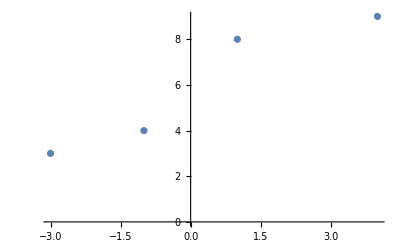

```mathematica
ListPlot[{{-3,3},{-1,4},{1,8},{4,9}}]
```

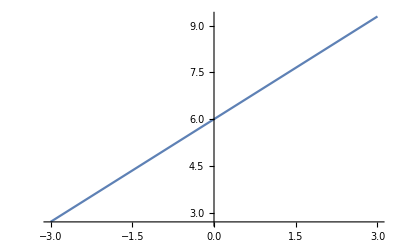

```mathematica
Plot[6+1.1t,{t,-3,3}]
```

### Problem 8.7

```mathematica
x={200,300,400,500,600,700,800,900};y={5.1,5.5,5.9,6.8,7.4,7.5,8.6,9.4};
Aconstant[x,y]
Bconstant[x,y]
```

3.68571

0.00607143

```mathematica
981/(0.00607143 1000)//N
```

161.576

Final answers:
	l_0=3.69 cm
	k=162 N/cm

### Problem 8.13

#### (a)

```mathematica
x={-3,-1,1,3};y={4,7.5,10.3,12};
Aconstant[x,y]
Bconstant[x,y]
SigmaY[x,y]
```

8.45

1.34

0.639531

8±t

s_0=8.5 m
v=1.3 m/s
σ_s=0.6 m

#### (b)

Sí, sus datos y incertezas son consistentes con la hipótesis de que la velocidad es constante.

#### (c)

En este caso las incertezas en la medida de la posición es inconsistente con el valor calculado de σ_s. Por lo tanto, no es consistente la hipótesis de que la velocidad sea constante.

### Problem 8.15

```mathematica
x=Range[6];y={5,14.4,23.1,32.3,41,50.4};
Aconstant[x,y]
SigmaA[x,y]
Bconstant[x,y]
SigmaB[x,y]
SigmaY[x,y]
```

-3.9

0.189486

9.02857

0.0486554

0.20354

Constants in least squares: 
	A=-3.9±0.2
	B=9.03±0.05

s=(-3.9±0.2)+(9.03±0.05)n

Therefore, 
	λ/2=s(n+1)-s(n)=9.03±0.05
	λ=18.1±0.1

## Chapter 9: Covariance and Correlation

### Definitions

```mathematica
covariance[x_,y_]:=Total[(x-ConstantArray[mean[x],Length[x]])(y-ConstantArray[mean[y],Length[y]])]/Length[x]//N
correlationCoefficient[x_,y_]:=covariance[x,y]/(standardDeviation2[x]standardDeviation2[y])
```

### Exercises

#### Example

```mathematica
α={35,31,33,32,34};β={50,55,51,53,51};covariance[α,β]
√(standardDeviation2[α]^2+standardDeviation2[β]^2+2covariance[α,β])
```

-2.4

0.632456

#### Quick Check 9.1

```mathematica
x={25,27,29};y={33,34,38};
covariance[x,y]
```

3.33333

```mathematica
x={25,27,29};y={33,34,38};
√(standardDeviation2[x]^2+standardDeviation2[y]^2+2covariance[x,y])
```

3.74166

```mathematica
x={25,27,29};y={33,34,38};
√(standardDeviation2[x]^2+standardDeviation2[y]^2)
```

2.70801

#### Quick Check 9.2

```mathematica
x={25,27,29};y={33,34,38};
correlationCoefficient[x,y]
```

0.944911

#### Quick Check 9.3

La probabilidad de que se obtenga un coeficiente de correlación r=0.6 de datos de dos variables no correlacionadas es de 0.5%. Esto significa que la correlación es altamanete significativa. En otras palabras, no hay duda para asegurar que las variables están correlacionadas.

#### Problem 9.1

```mathematica
x={20,23,23,22};y={30,32,35,31};
covariance[x,y]
```

1.75

#### Problem 9.3

(a)

```mathematica
x={20,23,23,22};y={30,32,35,31};
standardDeviation2[x]^2
standardDeviation2[y]^2
covariance[x,y]
```

1.5

3.5

1.75

(b)

```mathematica
x={20,23,23,22};y={30,32,35,31};
√(standardDeviation2[x]^2+standardDeviation2[y]^2+2covariance[x,y])
```

2.91548

(c)

```mathematica
x={20,23,23,22};y={30,32,35,31};
√(standardDeviation2[x]^2+standardDeviation2[y]^2)
```

2.23607

(d)

```mathematica
standardDeviation2[x+y]
```

2.91548

Sí. Se corroborá que es igual al resultado obtenido en el inciso (b).

#### Problem 9.9

```mathematica
x={1,2,3,5,6,7};y={5,6,6,8,8,9};
correlationCoefficient[x,y]
```

0.981981

#### Problem 9.11

(a) r=0.7, N=5. La probabilidad de obtener r=0.7 de mediciones de dos variables no correlacionadas es del 19%. La correlación no es significante. 

(b) r=0.7, N=20. La probabilidad de obtener r=0.7 de mediciones de dos variables no correlacionadas es del 0.1%. La correlación es altamente significante. Por lo tanto, no hay duda para creer que las variables sí están correlacionadas.

#### Problem 9.13

```mathematica
father={74,83,85,96,98,100,106,107,120,124};son={76,103,99,109,111,107,91,101,120,119};
Length[son]
correlationCoefficient[father,son]
```

10

0.727808

La correlación entre las dos variables es de r=0.7. La probabilidad de que medidas de variables no correlacionadas den como resultado ese coeficiente de correlación es del 2.4% para 10 datos. La correlación es significante.

## Chapter 10: The Binomial Distribution

### Definitions

```mathematica
binomialDistribution[n_,ν_,p_]:=Binomial[n,ν] p^ν(1-p)^(n-ν)
```

### Exercises

#### 10.19

Hipótesis: los skis lustrados no hacen ninguna diferencia. Esto implica que los skis lustrados y no lustrados tienen igual probabilidad (p=0.5) de ganar.

```mathematica
100*binomialDistribution[10,9,0.5]
```

0.976563

Existe menos del 1% de probabilidad de que los skis lustraods ganen 9 de 10 carreras. Por lo tanto, los resultados son significativos para concluir que la hipótesis es incorrecta y lustrar los skis sí hace una diferencia. Esto es válido tanto para el nivel de 1% y 5% de significancia.

#### 10.20

```mathematica
Total[100*binomialDistribution[14,#,0.5]&/@Range[12,14]]
```

0.646973

Hay menos del 1% de probabilidad de que 12 (o más) de las 14 plantas estuvieran más sanas sin el fertilizante no hiciera una diferencia. Esto sugiere que 12 o más plantas sanas de un total de 14 son datos altamente significativos (1% de significancia) para refutar la hipótesis inicial.

## Chapter 12: The Chi-Squared Test for a Distribution

#### Notas

- El chi cuadrado sirve para probar si la hipótesis respecto a la distribución estadística que obedece un set de datos. 
-